#### Example from page 22-23 of Wright, S. 1955. Cold Spring Harbor Symposia on Quantitative Biology 20:16–24.

```mathematica
Δq[q_]:=(q(1-q)^2(s1 q^2-s2(1-q^2)))/(q^2(1+s1 q^2)+2q(1-q)(1+s1 q^2)+(1-q)^2(1+s2(1-q^2)))
Wbar[q_]:=1+(s1+s2)q^2(1-q^2)
```

```mathematica
Solve[Δq[q]==0,q]//Simplify[#,Assumptions->s1<0∧s2<0]&
```

{{q→0},{q→1},{q→1},{q→-√(s2/(s1+s2))},{q→√(s2/(s1+s2))}}

```mathematica
FullSimplify[D[Δq[q],q]/.q->√(s2/(s1+s2)),Assumptions->s1<0∧s2<0]
```

(2 s2 (s1+2 (s2+√(s2 (s1+s2)))))/(s1+s2+s1 s2)

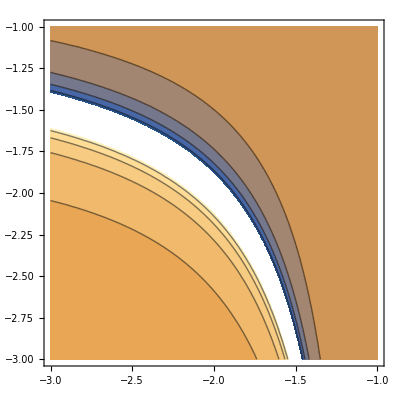

```mathematica
ContourPlot[(2 s2 (s1+2 (s2+√(s2 (s1+s2)))))/(s1+s2+s1 s2),{s1,-3,-1},{s2,-3,-1}]
```

```mathematica
Solve[D[Wbar[q],q]==0,q]
```

{{q→0},{q→-1/(√2)},{q→1/(√2)}}

```mathematica
D[Wbar[q],q,q]/.{q->1/(√2)}
```

s1+s2-5 (s1+s2)

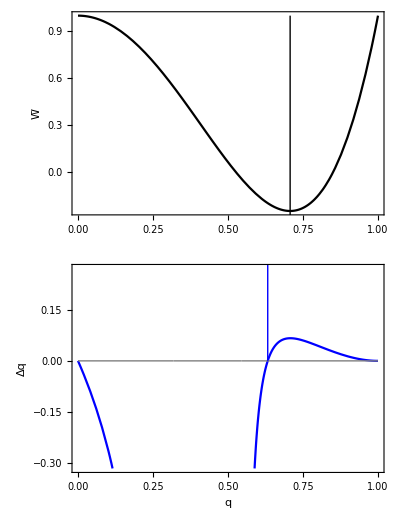

```mathematica
Function[{ss1,ss2},
GraphicsColumn[
{Plot[Evaluate[{Wbar[q]}/.{s1->ss1,s2->ss2}],{q,0,1},Axes->None,Frame->{{True,False},{True,False}},PlotStyle->{Black},FrameLabel->{None,W̄},Epilog->{Black,Line[{{1/(√2),-1},{1/(√2),1}}]}],
Plot[Evaluate[{Δq[q],0}/.{s1->ss1,s2->ss2}],{q,0,1},PlotRange->Automatic,Axes->None,Frame->{{True,False},{True,False}},PlotStyle->{Blue,Directive[Gray,Thin]},FrameLabel->{q,Δq},Epilog->{Blue,Line[{{√(ss2/(ss1+ss2)),0},{√(ss2/(ss1+ss2)),1}}]}]}]][-3, -2]
```